## Model

### introduction

The model can either be imported from stru/csv file, or created in Mathematica by DataSet. 

The working directory was set to be the Notebook directory.

### codes

```mathematica
SetDirectory[NotebookDirectory[]];

(* This is a particular defined function to deal with the improted stru files *)
editor1[list_]:=Module[{part1,part2,result},(
part1=StringSplit[First[list]];
part2=Drop[list,1];
result=Join[part1,part2])];

(* The localFileName refers to the name of genereated stru file by DISCUS *)
convertor[filein_,fileout_]:=Module[{localFileName,OldData,NewData,NewData2,dataset,Infile,Outfile},

Infile=ToString[filein];
localFileName=FileNameJoin[{Directory[],Infile}];

If[FileExistsQ[localFileName]==True,
(* Below code generates a new csv file in the Notebook Directory *)
OldData=Import[localFileName,"CSV"];
OldData=Flatten[OldData,{1}];
OldData=OldData[[4;;-1]];
NewData=editor1[#]&/@OldData;
NewData=Take[#,5]&/@NewData;

Outfile=ToString[fileout];
NewData2=Export[NotebookDirectory[]<>Outfile,NewData,"CSV"];

Print[Row[{"The DataSet file ",Outfile," was created from ",Infile, 
". It can be readily improted into Mathematica by SemanticImport"}]];

dataset=SemanticImport[NewData2,<|1->String,2->Automatic,3->Automatic,4->Automatic,5->Automatic|>];

dataset=dataset//Transpose//Prepend["i"->Table[x,{x,1,dataset[All,1]//Length}]]//Transpose,

Print[Row[{"The Document ",Infile," does not exist"}]]]];
```

### use case

```mathematica
convertor["happy","test1.csv"]
```

The Document happy does not exist

```mathematica
(* This is a Zr 3x3x3 model, there are 27 unit cells and each unti cell contains a Zr atom *)
Zr333=convertor["zr333.stru","zr333.csv"]
```

The DataSet file zr333.csv was created from zr333.stru. It can be readily improted into Mathematica by SemanticImport

Dataset[<>]

```mathematica
(* This is a Ca unit cell, which contains 12 atoms *)
Caf2unit=convertor["caf2unit.stru","caf2unit.csv"]
```

The DataSet file caf2unit.csv was created from caf2unit.stru. It can be readily improted into Mathematica by SemanticImport

Dataset[<>]

## Reference Pattern

### codes

```mathematica
SetDirectory[NotebookDirectory[]];

(* or use this code to get the orginal dataset for plotting *)
pdfdata[file_]:=Module[{localFileName,filename,oridata,newdata,output},(
filename=ToString[file];
localFileName=FileNameJoin[{Directory[],filename}];

If[FileExistsQ[localFileName]==True,
oridata=SemanticImport[filename];
oridata=Drop[oridata,None,{3,4}],

Print[Row[{"The Document '",filename,"' does not exist"}]]])]


pdfplot[file_,color_]:=Module[{localFileName,filename,oridata,newdata,output},(
filename=ToString[file];
localFileName=FileNameJoin[{Directory[],filename}];

If[FileExistsQ[localFileName]==True,
oridata=SemanticImport[filename];
oridata=Drop[oridata,None,{3,4}]//Normal;
output=ListLinePlot[oridata,PlotRange->All,PlotLabel->StringDelete[filename,".pdf"],PlotStyle->color],

Print[Row[{"The Document '",filename,"' does not exist"}]]])]
```

### use cases

```mathematica
pdfdata["zr333.pdf"]
```

Dataset[<>]

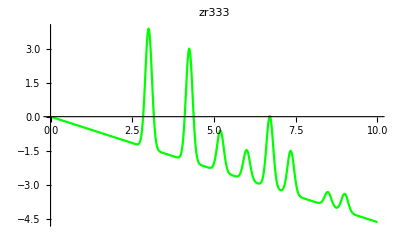

```mathematica
zr333ref=pdfplot["zr333.pdf",Green]
```

one can edit the raw PDF data and use ListLinePlot to plot the PDF in specific range of r.

## Unit cell Parameters

This code describes the unit cell parameters.

```mathematica
cellpara[file_,i_]:=Module[{localfilename,x,string1,result},(
localfilename=FileNameJoin[{Directory[],ToString[file]}];
x=Import[localfilename];

string1=First[StringCases[x, "cell"~~Shortest[n__]~~"\n"]];
string1=StringDelete[StringDelete[string1,"cell"],"\n"];
string1= StringSplit[string1," "];
string1=If[SyntaxQ[#],ToExpression[#],#]&/@string1;
string1=If[NumberQ[#],#,Nothing]&/@string1;
result=Part[string1,i];
Return[result]
)]
```

The six unit cell parameters of a unit cell can be loaded using:

```mathematica
cellpara["p.cll"]
```

{3.,3.,3.,90.,90.,90.}

```mathematica
(* 1-6 refers to a,b,c,α,β and γ,respectively.*)
cellpara["p.cll",1]
```

3.

## Calculation of PDF

### Introduction

Before the calculation, the unit cell information should be input.

```mathematica
Import["p.cll"]
```

title Dummy structure
spcgr P1
cell  3.00  3.00  3.00  90.0 90.0 90.0
atoms 
ZR    0.00  0.00  0.00  0.4

Assign a unit cell by:

```mathematica
(*unitcell=Input[]*)
(* In this case, the unit cell was assign to be one Zr atom *)

unitcell="p.cll";
```

```mathematica
a=cellpara[unitcell,1];
b=cellpara[unitcell,2];
c=cellpara[unitcell,3];
α=cellpara[unitcell,4]Degree;
β=cellpara[unitcell,5]Degree;
γ=cellpara[unitcell,6]Degree;
Vp=a*b*c*√(1-Cos[α]^2-Cos[β]^2-Cos[γ]^2+2*Cos[α]*Cos[β]*Cos[γ]);

Print[Labeled[a,"a"], Labeled[b  ,"b"],  Labeled[c,"c"],  Labeled[α,"α"],  Labeled[β,"β"],  Labeled[γ,"γ"],Labeled[Vp,"Volumn"]]
```

3.a3.b3.c1.5708α1.5708β1.5708γ27.Volumn

Then Assign a model by:

```mathematica
model=convertor["zr333.stru","zr333.csv"]
```

The DataSet file zr333.csv was created from zr333.stru. It can be readily improted into Mathematica by SemanticImport

Dataset[<>]

### codes

```mathematica
(* The unit of Scattering length is fm, 10^-15m, this code reflects the scattering length of atom i, this function will be further appended in the future*)
scatlength[i_]:=
If[model[i]["atoms"]=="ZR",7.16,
If[model[i]["atoms"]=="CA",4.70,
If[model[i]["atoms"]=="F",5.654]]];


(* The temperature factor of atom i in the model *)
Bfactor[i_]:=model[i]["Biso"];


(* This code returns the total number of atoms in the model *)
Num=Max[Normal[model[All, "i"]]];


vectorlist=Values[Normal[model[All,{"x","y","z"}]]];
vectorn[i_]:=Part[vectorlist,i];
diffvector[i_,j_]:=vectorn[j]-vectorn[i];


(* This code describe the distance between two atoms i and j in the model *)
distanceij[i_,j_]:=√(a^2 Part[diffvector[i,j],1]^2+b^2 Part[diffvector[i,j],2]^2+c^2 Part[diffvector[i,j],3]^2+2*a*b*Cos[γ]*Part[diffvector[i,j],1]*Part[diffvector[i,j],2]+2*a*c*Cos[β]*Part[diffvector[i,j],1]*Part[diffvector[i,j],3]+2*b*c*Cos[α]Part[diffvector[i,j],2]*Part[diffvector[i,j],3])

(* Gaussian peak width sigma of the model *)
delta=0.0;
sigma[i_,j_]:=√((Bfactor[i]+Bfactor[j])/(8*π^2));

(* If the delta modification was applied, the functin should be;
sigma[model_,i_,j_]:=√((Bfactor[i]+Bfactor[j])/(8*π^2))-delta/distanceij[model,i,j]^2   *)

(* The average scattering length of the model *)
meanb=Sum[scatlength[i],{i,1,Num}]/Num;

(* This is the weight correction which based on the atoms of the pair i,j *)
Acomponent[i_,j_]:=(scatlength[i]*scatlength[j])/meanb^2;

(* The number density of the model *)
(* The numbertor should be the number of atoms in one unit cell *)
ρ0=Rationalize[1/Vp];


(* This is the most improtant part of the function, which reflects the local Gaussian distribution *)
Tcomponent[r_,i_,j_]:=PDF[NormalDistribution[distanceij[i,j],sigma[i,j]],r];

pairset=Subsets[Table[x,{x,1,Num}],{2}];
pdfs2[{i_,j_}]:=Tcomponent[r,i,j]*(scatlength[i]*scatlength[j])/meanb^2;


background[r_] :=-4π*r*ρ0;


rawfunc=Total[pdfs2/@pairset]*2;

(*This code will produce the Matamatical expression of the PDF with the distance "r" *)
PDFcalc[r_]:=rawfunc/(r*Num)+background[r];


(* Multiply the result with the Bcomponent to simulate the experimental resolution effect *)
resolution=0.00;
Bcomponent[r_]:=Exp[-(r*resolution)^2/2];
```

### use cases

```mathematica
Timing[PDFcalc[r]]
```

{0.,1/(27 r)2 (15.8533 ⅇ^(-49.348 (-10.3923+r)^2)+95.1199 ⅇ^(-49.348 (-9.+r)^2)+71.3399 ⅇ^(-49.348 (-8.48528+r)^2)+190.24 ⅇ^(-49.348 (-7.34847+r)^2)+285.36 ⅇ^(-49.348 (-6.7082+r)^2)+107.01 ⅇ^(-49.348 (-6.+r)^2)+126.826 ⅇ^(-49.348 (-5.19615+r)^2)+285.36 ⅇ^(-49.348 (-4.24264+r)^2)+214.02 ⅇ^(-49.348 (-3.+r)^2))-(4 π r)/27}

It takes 0.6s to produce the expression of PDF of Zr 3x3x3 model. Then one can simply use the plot function in Mathematica to plot it.

General::munfl: Exp[-5329.38] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3997.01] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3552.89] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

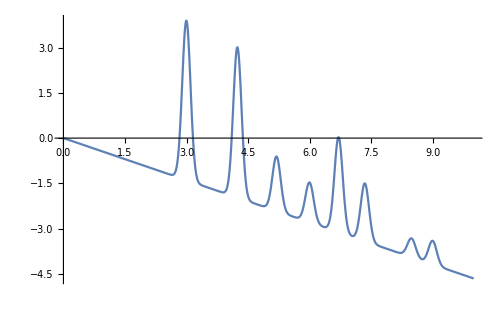

```mathematica
figure1=Plot[PDFcalc[r],{r,0,10}]
```

```mathematica
(* Comparsion with a reference *)
```

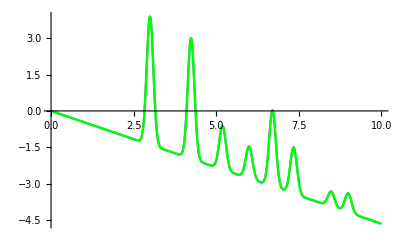

```mathematica
Show[figure1,zr333ref]
```

Setting Details

Q termination : Not applied                  (Convolution with (Sin(Q_max*r))/r)
Instrument resolution : Not applied
Convolution with therm Gauss : Applied
Resolution Broadening : 0.0                  (Term B_k, see PDFFIT user guide pp48)

Quad correlation factor : 0.0
Linear correlation factor : 0.0

Delta correction of peak width : 0.0  (Apply this modification may increase the calculation time by 2 times)   
Peak Sharpening: Not Applied